```mathematica
ClearAll["Global`*"]
```

## N = 60

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=30
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
ten := 3.72 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {29.3171} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {20.9687} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {29.3171} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {29.3171} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

InterpolatingFunction::dmval: Input value {3.79639×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

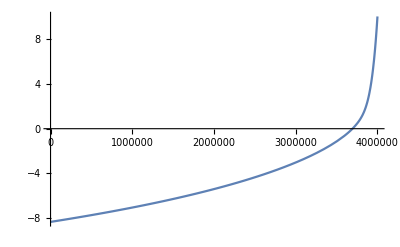

```mathematica
Plot[ϕ[t]-ϕend,{t,0,4 10^6},PlotRange->All]
```

```mathematica
tend
```

3.69425×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
```

```mathematica
ϕ[hc[0.05]]
```

21.4615

```mathematica
k:=0.00009
Timing[PS[k]]
```

{4.,2.48334×10^-9}

```mathematica
k:=0.05
Timing[PS[k]]
```

{12.1875,2.13298×10^-9}

```mathematica
k:=0.002
Timing[r[k]]
```

{10.1875,0.0315542}

## Extracting PS(k) N =60

```mathematica
list =Parallelize[Table[{k,PS[k]},{k,0.0001,0.1,0.0001}]];
list1  = Parallelize[Table[{k,PS[k]},{k,0.1+0.01,2.5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data\\k_vs_PS(k)_mu=30.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data\k_vs_PS(k)_mu=30.dat

```mathematica
(*strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.0001,0.1,0.0001}]]*)
Parallelize[For[i=0,i<1000,Write[strm,k=N[i/10000],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.1+0.01,2.5,0.01}]]*)
Parallelize[For[i=10,i<231,Write[strm,k=N[i/100],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];*)
```

## Fitting PS(k) N =60

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=30.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot]+ β/6 (Log[k/kpivot])^2),{AS,spec, α, β},k]
```

FittedModel[2.12573×10^-9 ⅇ^(-0.098037+0.000105991 Log[20. k]^2) k^(-0.0339425-0.000406219 Log[20. k]+0.0000353806 Log[20. k]^2)]

```mathematica
Normal[%]
```

2.12573×10^-9 ⅇ^(-0.098037+0.000105991 Log[20. k]^2) k^(-0.0339425-0.000406219 Log[20. k]+0.0000353806 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→2.1335×10^-9,spec→0.967274,α→-0.000812437,β→0.000212284}

```mathematica
PPS[k_]:=2.1257347156341786*^-9 ⅇ^(-0.09803698791053564+0.00010599084457660767 Log[20. k]^2) k^(-0.033942473096760004-0.0004062187303908125 Log[20. k]+0.000035380613118296215 Log[20. k]^2)
dPPS[k_]=D[PPS[k],{k,1}];
nnS[k_]=1+k/PPS[k] dPPS[k];
```

```mathematica
PPS[0.05]
```

2.1335×10^-9

```mathematica
nnS[0.002/0.05]
```

0.967461

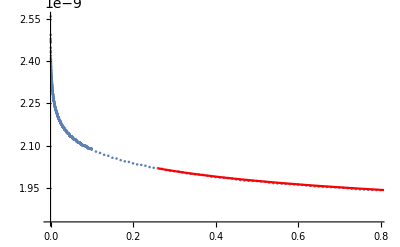

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPS[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1 , plot2}]
```

```mathematica
fit["RSquared"]
```

0.999998

## Extracting PT(k) N =60

```mathematica
list =Parallelize[Table[{k,PT[k]},{k,0.001,0.1,0.002}]];
list1  = Parallelize[Table[{k,PT[k]},{k,0.1+0.01,5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=30.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data_PT\k_vs_PT(k)_mu=30.dat

## Fitting PT(k) N =60

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=30.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot]+ β/6 (Log[k/kpivot])^2),{AS,spec, α, β},k]
```

FittedModel[9.17112×10^-12 ⅇ^(-0.0134333-0.0000110409 Log[20. k]^2) k^(-0.00469707-0.0000710709 Log[20. k]-3.68554×10^-6 Log[20. k]^2)]

```mathematica
Normal[%]
```

9.17112×10^-12 ⅇ^(-0.0134333-0.0000110409 Log[20. k]^2) k^(-0.00469707-0.0000710709 Log[20. k]-3.68554×10^-6 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→9.17697×10^-12,spec→0.995516,α→-0.000142142,β→-0.0000221133}

```mathematica
PPT[k_]:=9.171116074455623*^-12 ⅇ^(-0.01343334286695645-0.000011040898129752875 Log[20. k]^2) k^(-0.004697069450106568-0.00007107091653145296 Log[20. k]-3.6855423387532865*^-6 Log[20. k]^2)
dPPT[k_]=D[PPT[k],{k,1}];
nnT[k_]=k/PPT[k] dPPT[k];
```

```mathematica
PPT[0.05]
```

9.17697×10^-12

```mathematica
nnT[0.002/0.05]
```

-0.00445299

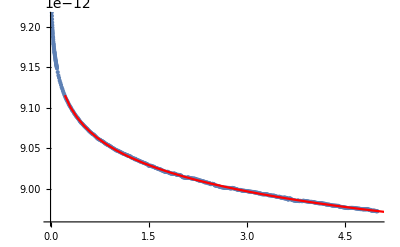

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPT[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1 , plot2}]
```

```mathematica
fit["RSquared"]
```

## Calculation r(k) N = 60

```mathematica
8 PPT[0.002]/PPS[0.002]
```

0.0315712

## N = 50

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-50==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

```mathematica
μ:=30
M := Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N50.csv"][[μ,2]];
p:=4
ϕend:=First[cend[p,μ]]
ϕini:=First[cini[p,μ]]
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
ten := 2.72 10^6
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,-90000,ten},MaxSteps->100000,AccuracyGoal->10];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,ten *0.9}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

CompiledFunction::cfse: Compiled expression {29.3171} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {21.6065} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {29.3171} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {29.3171} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

InterpolatingFunction::dmval: Input value {2.72789×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

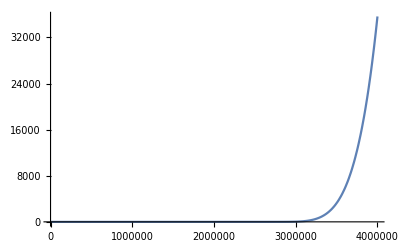

```mathematica
Plot[ϕ[t]-ϕend,{t,0,4 10^6},PlotRange->All]
```

```mathematica
tend
```

2.67177×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500,1000}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500,1000}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}]
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
```

```mathematica
ϕ[hc[0.05]]
```

22.1614

```mathematica
k:=0.00009
Timing[PS[k]]
```

{4.125,1.82258×10^-9}

```mathematica
k:=0.05
Timing[PS[k]]
```

{9.75,2.14267×10^-9}

```mathematica
k:=0.002
Timing[r[k]]
```

{9.40625,0.0415979}

## Extracting PS(k) N =50

```mathematica
list =Parallelize[Table[{k,PS[k]},{k,0.001,0.1,0.002}]];
list1  = Parallelize[Table[{k,PS[k]},{k,0.1+0.01,5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=30_N50.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data_PS\k_vs_PS(k)_mu=30_N50.dat

```mathematica
(*strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.0001,0.1,0.0001}]]*)
Parallelize[For[i=0,i<1000,Write[strm,k=N[i/10000],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];
strm=OpenWrite["C:\\Users\\RAUL\\Downloads\\dat.dat",FormatType->OutputForm];
(*Parallelize[Do[Write[strm,k,"   ",CForm[Re[PS[k]]]],{k,0.1+0.01,2.5,0.01}]]*)
Parallelize[For[i=10,i<231,Write[strm,k=N[i/100],"   ",CForm[Re[PS[k]]]],i++]]
Close[strm];*)
```

## Fitting PS(k) N =50

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PS\\k_vs_PS(k)_mu=30_N50.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot]+ β/6 (Log[k/kpivot])^2),{AS,spec, α, β},k]
```

FittedModel[2.13634×10^-9 ⅇ^(-0.11666-0.0000744552 Log[20. k]^2) k^(-0.0400178-0.000359094 Log[20. k]-0.0000248538 Log[20. k]^2)]

```mathematica
Normal[%]
```

2.13634×10^-9 ⅇ^(-0.11666-0.0000744552 Log[20. k]^2) k^(-0.0400178-0.000359094 Log[20. k]-0.0000248538 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→2.14323×10^-9,spec→0.961058,α→-0.000718189,β→-0.000149123}

```mathematica
PPS[k_]:=2.136338109505285*^-9 ⅇ^(-0.11665995063177349-0.00007445524299426055 Log[20. k]^2) k^(-0.04001779891622475-0.00035909440644030433 Log[20. k]-0.000024853770696247995 Log[20. k]^2)
dPPS[k_]=D[PPS[k],{k,1}];
nnS[k_]=1+k/PPS[k] dPPS[k];
```

```mathematica
PPS[0.05]
```

2.14323×10^-9

```mathematica
nnS[0.002/0.05]
```

0.961214

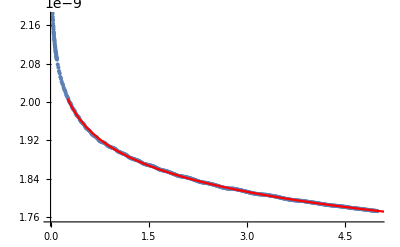

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPS[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1 , plot2}]
```

```mathematica
fit["RSquared"]
```

1.

## Extracting PT(K) N = 50

```mathematica
list =Parallelize[Table[{k,PT[k]},{k,0.001,0.1,0.002}]];
list1  = Parallelize[Table[{k,PT[k]},{k,0.1+0.01,5,0.01}]];
list2 = Union[list,list1];
Export["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=30_N50.dat",list2]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Approach fitting PS\data_PT\k_vs_PT(k)_mu=30_N50.dat

## Fitting PT(k) N =50

```mathematica
powerspectra:=Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Approach fitting PS\\data_PT\\k_vs_PT(k)_mu=30_N50.dat","Table"]
```

```mathematica
Clear[k,kpivot]
```

```mathematica
kpivot:=0.05
```

```mathematica
fit=NonlinearModelFit[powerspectra,AS(k/kpivot)^(spec-1+1/2 α Log[k/kpivot]+ β/6 (Log[k/kpivot])^2),{AS,spec, α, β},k]
```

FittedModel[1.22784×10^-11 ⅇ^(-0.0179749-0.0000166866 Log[20. k]^2) k^(-0.0062982-0.0000994817 Log[20. k]-5.57011×10^-6 Log[20. k]^2)]

```mathematica
Normal[%]
```

1.22784×10^-11 ⅇ^(-0.0179749-0.0000166866 Log[20. k]^2) k^(-0.0062982-0.0000994817 Log[20. k]-5.57011×10^-6 Log[20. k]^2)

```mathematica
fit["BestFitParameters"]
```

{AS→1.22894×10^-11,spec→0.994,α→-0.000198963,β→-0.0000334207}

```mathematica
PPT[k_]:=1.2278423807859684*^-11 ⅇ^(-0.017974938944057776-0.000016686573245328094 Log[20. k]^2) k^(-0.006298202710533075-0.00009948174829892373 Log[20. k]-5.570114990793872*^-6 Log[20. k]^2)
dPPT[k_]=D[PPT[k],{k,1}];
nnT[k_]=k/PPT[k] dPPT[k];
```

```mathematica
PPT[0.05]
```

1.22894×10^-11

```mathematica
nnT[0.002/0.05]
```

-0.00595662

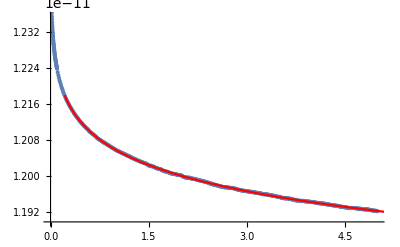

```mathematica
plot1:=ListPlot[powerspectra]
plot2:=Plot[PPT[k],{k,0,10},PlotStyle->{Red}]
Show[{ plot1 , plot2}]
```

```mathematica
fit["RSquared"]
```

1.

## Calculation r(k) N =50

```mathematica
8 PPT[0.002]/PPS[0.002]
```

0.0413418

FAlta N = 60